# Top 600 NFT Collections (SOL)

## Getting, Understanding, and Preprocessing the Data

### Getting the Data:

```mathematica
ds = Import["/Users/bilalsyed/Downloads/NFT_Top_Collections.csv", "Dataset","HeaderLines"->1];
```

```mathematica
ds[1;;10,All]
```

### Understanding the Data:

- Name: The name of the NFT collection.
- Volume: The volume of sales from the NFT collection (in SOL and USD).
- Market Cap: The market capitalization—total value of the collection’s items in circulation (in SOL and USD).
- Sales: The number of sales from the NFT collection.
- Floor_Price: The lowest price of any NFT in the collection (in SOL and USD).
- Average_Price: The average price of an NFT in the collection (in SOL and USD).
- Owners: The number of owners of NFT’s in the collection.
- Assets: The number of items in the collection.
- Owner Asset Ratio: The ownership percentage of all items in the collection.
- Category: The category of the NFT collection.
- Website: The associated website of the NFT collection.
- Logo: The associated image’s weblink of the NFT collection.

### Functions to Add Logo Images to the Dataset:

The last column of our dataset has a weblink to the logo of the NFT. I am importing it in Mathematica to get the image.

The functions ‘logos’ reads each row of the last column ‘Logo’ and Imports it.

```mathematica
logos[data_] := Table[Import[data[i,Last]],{i,1,Length[data]}]
```

The following function calls the logos function and adds them to the end of our dataset.

```mathematica
addLogosToDataset[data_,logos_]:= data//Transpose//Append["Logo"->logos]//Transpose;
```

### Preprocessing the Data:

```mathematica
Dimensions[ds]
```

{592,17}

### To check whether our dataset is having duplicates or not:

```mathematica
DuplicateFreeQ[ds]
```

True

### Calculating number of missing values and dealing with it:

Creating a separate clean dataset ‘cds’:

Empty cells have an empty string in them. To use the DeleteMissing[ ] function, we first need to convert them to Missing[ ].

```mathematica
cds=ds/.""->Missing[];
```

```mathematica
mv=Table[Count[cds[[All,i]],_Missing],{i,1,17}]
```

{0,0,0,0,0,0,0,48,48,0,0,0,0,49,282,111,1}

```mathematica
Total[mv]
```

539

Dropping Unnecessary Columns:
- Category (almost half of it is empty
- Website (we don’t really need it)

```mathematica
cds=Drop[cds,None,{15,16}];
```

```mathematica
Dimensions[cds]
```

{592,15}

Deleting Rows with Missing Values:

```mathematica
cds=DeleteMissing[cds,1,Infinity];
```

```mathematica
Dimensions[ cds]
```

{540,15}

#### Our new ‘clean’ dataset:

```mathematica
cds[1;;5]
```

## Correlation Analysis

```mathematica
corr = Table[Correlation[cds[All,i]//Normal,cds[All,j]//Normal]//N,{i,{4,6,7,9,11,12,13,14}},{j,{4,6,7,9,11,12,13,14}}]//Dataset;
```

The above line of code gives us the correlation table. To make it more readable, we are adding a column to the left and a dataset header.

Adding left column:

```mathematica
l = {"Volume USD","Market Cap USD","Sales","Floor Price USD","Avg Price USD","Owner","Assets","Owner Asset Ratio"};
```

```mathematica
corr = Dataset[Table[Prepend[Normal[corr[i,All]],l[[i]]],{i,1,8}]];
```

Adding header:

```mathematica
corr = corr[All,<|""->1,"Volume USD"->2,"Market Cap USD"->3,"Sales"->4,"Floor Price USD"->5,"Avg Price USD"->6,"Owner"->7,"Assets"->8,"Owner Asset Ratio"->9|>];
```

```mathematica
corr
```

### Analyzing our data with correlation table :

#### From the above, it is clear that the following have strong positive correlations (>0.5): - Volume & Avg Price [0.60] - Market Cap & Assets [0.53] - Sales & Owner [0.81] - Sales & Assets [0.75] - Owner & Assets [0.91] This simply means that an increase in one of them will lead to an increase in the other.

## Top 20 NFT Collections based on Market Cap

### Sorting the dataset by Market Cap and selecting the top 20 into ‘mc20’. Also, excluding SOL columns (can select either SOL or USD, one is enough):

```mathematica
mc20 = cds[SortBy["Market_Cap_USD"]]//Reverse;
mc20 = mc20[1;;20];
mc20 = addLogosToDataset[mc20,logos[mc20]];
mc20 = mc20[All,{2,4,6,7,9,11,12,13,14}];
```

```mathematica
mc20[1;;5]
```

#### Among the top 5 NFT collections with the highest market cap (the MOST money), the 1st, 4th and 5th are NSFW. People are spending around $200-$300 to buy it and its Market Cap is around $150k-$370k. Wow!

### Having a look at the Market Cap of the top 20 NFT Collections based on Market Cap:

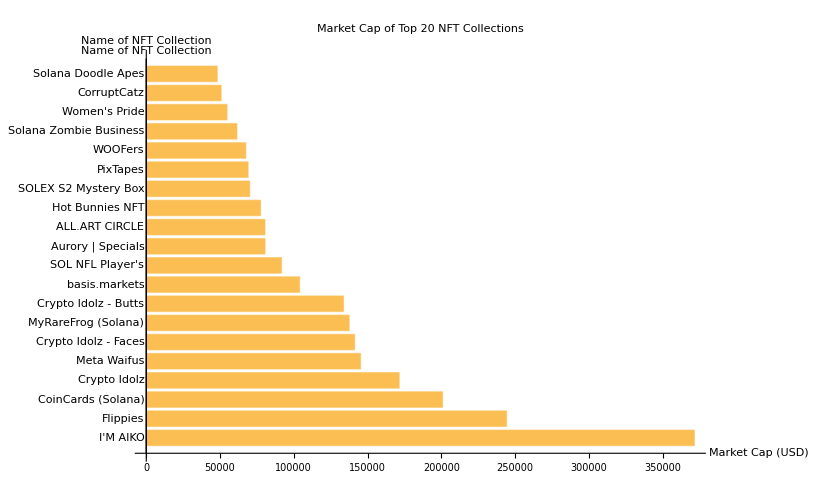

```mathematica
BarChart[mc20[All,3],ChartLabels->mc20[All,1]//Normal,BarOrigin->Left, AxesLabel->{"Name of NFT Collection","Market Cap (USD)"}, PlotLabel->"Market Cap of Top 20 NFT Collections"]
```

### What percentage of the total Market Cap is in the top 20? [61%]

```mathematica
Total[mc20[All,3]]*100/Total[cds[All,6]]
```

61.2616

#### So 3/5th of the Market Cap is held by just 20 NFT Collections out of almost 600.

### Let’s analyze their Average Price:

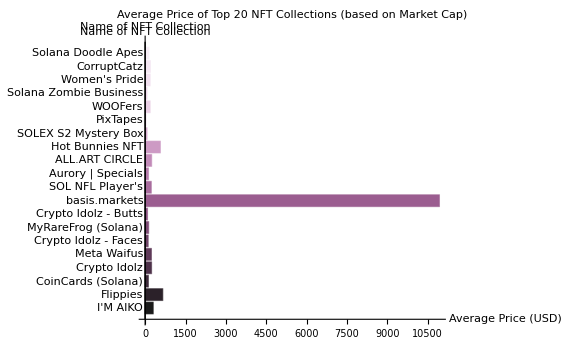

```mathematica
BarChart[mc20[All,6],ChartLabels->mc20[All,1]//Normal,BarOrigin->Left,ChartStyle->"FuchsiaTones",ImageSize->Large,AxesLabel->{"Name of NFT Collection","Average Price (USD)"},PlotLabel->"Average Price of Top 20 NFT Collections (based on Market Cap)"]
```

#### So, basis.markets has the highest average price [$10933.9]. Let’s see how the distribution is among the other 19 (exclude basis.markets).

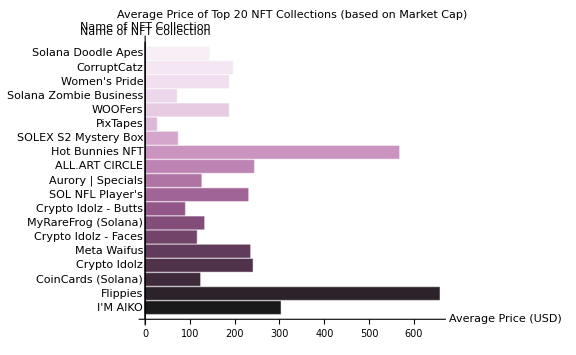

```mathematica
BarChart[mc20[{1,2,3,4,5,6,7,8,10,11,12,13,14,15,16,17,18,19,20},6],ChartLabels->mc20[{1,2,3,4,5,6,7,8,10,11,12,13,14,15,16,17,18,19,20},1]//Normal,BarOrigin->Left,ChartStyle->"FuchsiaTones",ImageSize->Large,AxesLabel->{"Name of NFT Collection","Average Price (USD)"},PlotLabel->"Average Price of Top 20 NFT Collections (based on Market Cap)"]
```

```mathematica
mc20[{1,2,3,4,5,6,7,8,10,11,12,13,14,15,16,17,18,19,20},6]//Normal//Mean
```

207.239

#### So, excluding basis.markets, the costliest is Flippies [$657.2], cheapest is PixTapes [$26] and the average is around $207.

Finding Distribution (just curious):

Top 20:

```mathematica
mc20[All,6]//FindDistribution
```

CauchyDistribution[154.168,76.045]

Top 20 (excluding basis.markets):

```mathematica
mc20[{1,2,3,4,5,6,7,8,10,11,12,13,14,15,16,17,18,19,20},6]//FindDistribution
```

GammaDistribution[1.67608,131.28]

## Top 20 NFT Collections based on Sales

### Sorting the dataset by Sales and selecting the top 20 into 'sales20‘. Also, excluding SOL columns:

```mathematica
sales20 = cds[SortBy["Sales"]]//Reverse;
sales20 = sales20[1;;20];
sales20 = addLogosToDataset[sales20,logos[sales20]];
sales20 = sales20[All,{2,4,6,7,9,11,12,13,14}];
```

```mathematica
sales20[1;;5]
```

### Having a look at the distribution of sales:

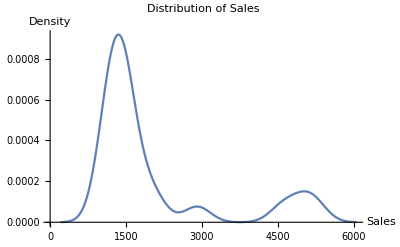

```mathematica
SmoothHistogram[sales20[All,4],AxesLabel->{"Sales","Density"}, PlotLabel->"Distribution of Sales"]
```

### What percentage of the total Sales is made by the top 20? [42%]

```mathematica
Total[sales20[All,4]]*100/Total[cds[All,7]]//N
```

42.17

#### 42% of the overall sales are made by just 20 NFT Collections.

### Let’s Analyze their Average Price:

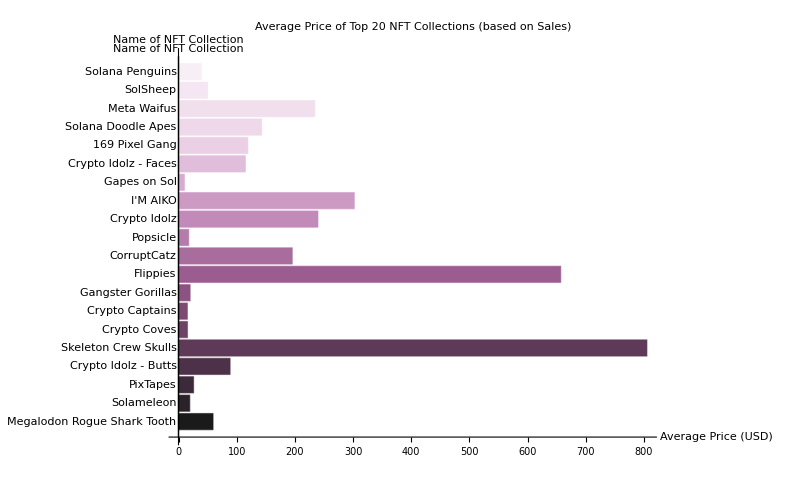

```mathematica
BarChart[sales20[All,6],ChartLabels->sales20[All,1]//Normal,BarOrigin->Left,ChartStyle->"FuchsiaTones",ImageSize->Large,AxesLabel->{"Name of NFT Collection","Average Price (USD)"},PlotLabel->"Average Price of Top 20 NFT Collections (based on Sales)"]
```

Having a look at the distribution (just curious!):

```mathematica
sales20[All,6]//FindDistribution
```

WeibullDistribution[0.468751,95.3258,10.2336]

```mathematica
sales20[All,6]//Mean
```

158.669

### Distribution of Average Price:

We wanted to get a deeper understanding of the average price of these top NFT Collections. A box plot would be great for this.

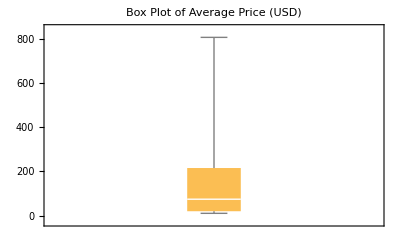

```mathematica
BoxWhiskerChart[sales20[All,6],PlotLabel->"Box Plot of Average Price (USD)"]
```

#### - This shows that people are spending between $10 and $805 on the top 20 NFT Collections (based on Sales). - On average, around $150 was being spent among top 20s. - The sales of 10 of the NFTs from the top 20s are just between $10 to $74. The remaining 10 had sales between $75 and $800. This is really interesting! - The majority (75%) of the sales were from around $10 to $215, while just 1/4th of the top 20 NFT Collections had sales between $215 and $800.

## Top 20 NFT Collections with Highest Number of Owners

### Sorting by Owners, selecting top 20, excluding SOL columns:

```mathematica
owners20 = cds[SortBy["Owners"]]//Reverse;
owners20  = owners20[1;;20];
owners20 = addLogosToDataset[owners20,logos[owners20]];
owners20 = owners20[All,{2,4,6,7,9,11,12,13,14,15}];
```

```mathematica
owners20[1;;5]
```

### A quick peak at the distribution of owners:

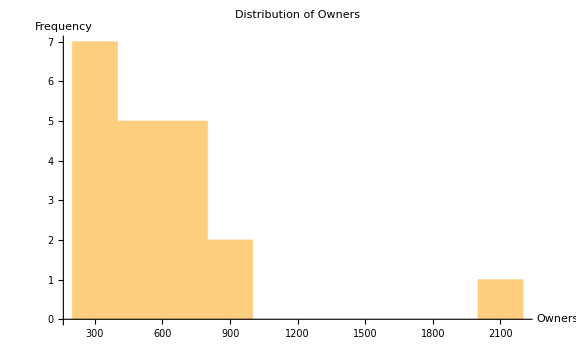
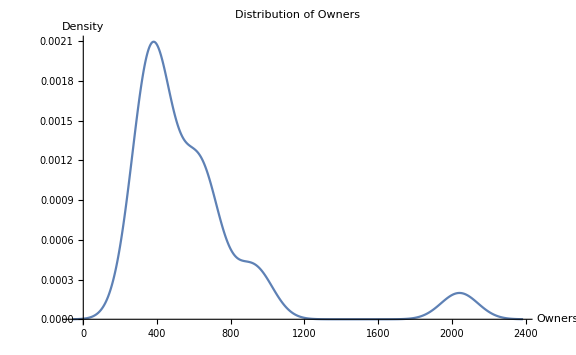

```mathematica
{Histogram[owners20[All,7],AxesLabel->{"Owners","Frequency"}, PlotLabel->"Distribution of Owners",ImageSize->Large],
SmoothHistogram[owners20[All,7],AxesLabel->{"Owners","Density"}, PlotLabel->"Distribution of Owners",ImageSize->Large]}
```

### What percentage of the total owners falls under the category of top 20 NFTs? [12.3 %]

```mathematica
Total[owners20[All,7]]*100/Total[cds[All,7]]//N
```

12.3364

How many total owners?

```mathematica
Total[cds[All,11]]
```

128267.

#### Only around 12% of the total owners (128, 267) have bought the top 20 NFTs.

### NFT Collection with most owners:

```mathematica
owners20[1]
```

Percentage of total owners owning Solameleon:

```mathematica
Total[owners20[1,7]]*100/Total[cds[All,7]]//N
```

2.13052

#### - “Solameleon” NFT has the highest number of owners, which constitutes approx 2% of the total owners. - They have the second highest number of sales as previously found, together with the above fact, making it the ‘Most Popular NFT’ among the population owning NFTs.

### As observed earlier, the number of owners seems to be highly correlated with the features such as "Assets" and "Sales". Let’s explore that further:

#### Correlation of Owners with Assets:

```mathematica
corr[7,6]
```

0.908035

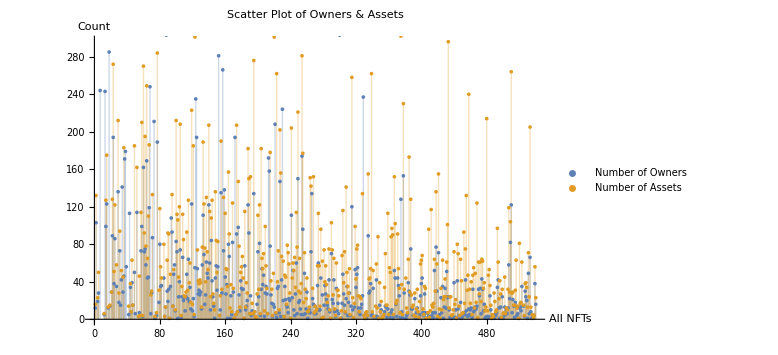

```mathematica
ListPlot[{cds[All,12],cds[All,13]},PlotStyle->Thick,PlotLegends->{"Number of Owners","Number of Assets"},Filling->Axis,AxesLabel->{"All NFTs","Count"}, PlotLabel->"Scatter Plot of Owners & Assets",ImageSize->Large]
```

#### Correlation of Owners with Sales:

```mathematica
corr[3,6]
```

0.810149

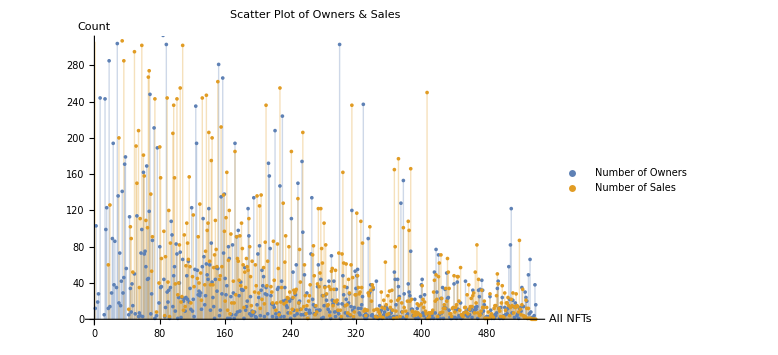

```mathematica
ListPlot[{cds[All,12],cds[All,7]},PlotStyle->Thick,PlotLegends->{"Number of Owners","Number of Sales"},Filling->Axis,AxesLabel->{"All NFTs","Count"}, PlotLabel->"Scatter Plot of Owners & Sales",ImageSize->Large]
```

### From the above visualizations and calculations, it shows a very strong correlation between ‘Owners’ & ‘Assets’ and ‘Owner’ & ‘Sales’. So the higher the Owners, the higher is the Assets and Sales.

## Categories

We wanted to analyse the categories of our NFT Collections. So we individually searched the top 100 NFT Collections (from our dataset) on solsea.io and divided them into the following categories:
- Collectible
- Digital Art
- PFP (Profile Picture)
- 3D
- Music
- P2E (Play 2 Earn)
- Metaverse

We then created the following excel file:

```mathematica
catds = Import["/Users/bilalsyed/Downloads/Top 100 with Categories.xlsx", "Dataset","HeaderLines"->1];
catds = catds[[1]];
```

```mathematica
catds[1;;5]
```

```mathematica
catds//Dimensions
```

{101,15}

```mathematica
c = catds[1;;100,Last]//Counts
```

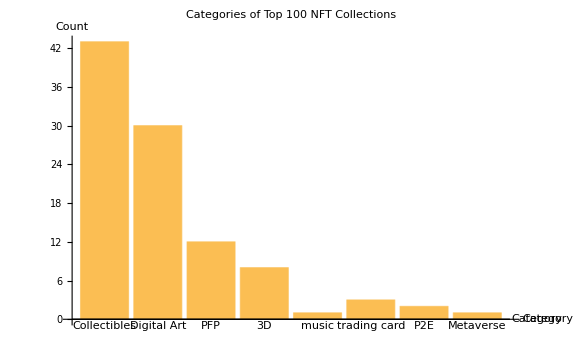

```mathematica
BarChart[c, ChartLabels->Keys[c]//Normal,ImageSize->Large,AxesLabel->{"Category","Count"},PlotLabel->"Categories of Top 100 NFT Collections"]
```

#### Clearly, ‘Collectibles’ and ‘Digital Art’ are the most popular categories.

## Failed Projects

#### Market Cap = 0 means it has failed. Might have made a few sales though before falling.

```mathematica
mcZero = Cases[KeyValuePattern["Market_Cap_USD"->0]]@ds[;;,{2,4,6,7,8,9,11,12,13,14}];
```

### Sorting by Sales:

This will bring the worst of the worst on top.

```mathematica
mcZero = mcZero[SortBy["Sales"]];
```

```mathematica
mcZero[1;;10]
```

### Quick analysis of these NFT Collection’s Sales:

```mathematica
s=mcZero[;;,4];
```

```mathematica
Max[s]
```

629

```mathematica
Min[s]
```

0

```mathematica
Mean[s]//N
```

44.2906

#### With Market Cap = 0: - The maximum and the minimum number of sales reported are 629 and 0, respectively. - The average number of sales reported are approximately 44.

### Number of NFT Collections with (market cap 0 and) zero sales:

```mathematica
t = Cases[KeyValuePattern["Sales"->0]]@mcZero;
```

```mathematica
Length[t]
```

9

#### -These NFTs have Owners, but no Sales. Possibly, the owners are the creators themselves.

### How many were complete failures (0 Sales) and how many failed after a while (MC 0 but with some sales)?

```mathematica
completeFailures = Cases[KeyValuePattern["Sales"->0]]@mcZero//Length;
failures = Length[Cases[KeyValuePattern["Market_Cap_USD"->0]]@mcZero]-completeFailures;
```

```mathematica
{completeFailures,failures}
```

{9,311}

### What % age are failures and complete failures?

```mathematica
{failures*100/Length[ds]//N,completeFailures*100/Length[ds]//N}
```

{52.5338,1.52027}

#### WOW!! Over half of the NFT projects failed!!

## Exclusive NFTs?

### Higher the Owner Asset Ratio, higher its diversity (more people own it). Lower = exclusive? What if they just weren’t successful? Check the sales/market cap.

```mathematica
oar = ds[SortBy["Owner_Asset_Ratio"]];
oar[All,{2,6,7,9,10,12,13,14}]
```

### Yep... Majority are failed projects (Market Cap 0). Let’s remove them.

```mathematica
oar = Query[Select[!MemberQ[{0},#"Market_Cap_USD"]&]]@oar;
oar = oar[1;;30];
oar = addLogosToDataset[oar,logos[oar]];
oar = oar[All,{2,6,7,9,10,12,13,14,17}];
```

```mathematica
oar[1;;10]
```

### So these are the 10 NFT Collections with the lowest Owner Asset Ratio. These must be the most exclusive ones!

```mathematica
oar[1;;10,Last]//Normal
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

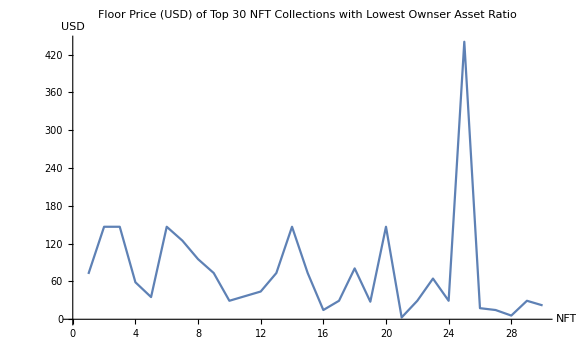

```mathematica
ListLinePlot[{oar[All,4]},AxesLabel->{"NFT","USD"},ImageSize->Large, PlotLabel->"Floor Price (USD) of Top 30 NFT Collections with Lowest Ownser Asset Ratio"]
```

#### From the above graph it seems majority of the people are willing to pay a maximum of $150 on NFTs which they might have an interest in and might want to buy, even though they are not popular or among the best performing. But, on further analysis:

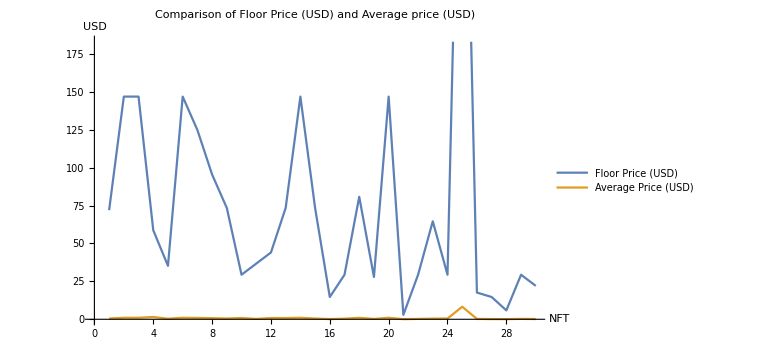

```mathematica
ListLinePlot[{oar[All,4],oar[All,5]},AxesLabel->{"NFT","USD"},PlotLegends->{"Floor Price (USD)","Average Price (USD)"},ImageSize->Large, PlotLabel->"Comparison of Floor Price (USD) and Average price (USD)"]
```

#### Almost all have an average price of less than a dollar. Seems people bought it due to the price drop, just in case it goes back up and they can sell it for a profit. I had assumed a small portion of people bought these NFT Collections due to personal interest. Turns out, it was just a gamble.